NDSolve::impsagpg: Unable to satisfy the ImplicitSolver tolerances for AccuracyGoal and PrecisionGoal at l = 0.0240556.

{{h→InterpolatingFunction[…],g→InterpolatingFunction[…],Kc→InterpolatingFunction[…],Ks→InterpolatingFunction[…]}}

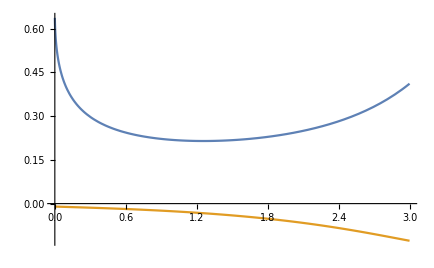

```mathematica
vperp=2;
omega=.01;
kc0=.5;
ks0=20;
pfc=4π/1;
pfs=4π/5;
Clear[h,g,Kc,Ks]
Dh[x_]:=2x
Dg[x_,y_]:=1/2(x+y+1/y)
sol=NDSolve[
{
(* the RG-flow *)
h'[l]-h[l]*(2-Dh[Ks[l]])-g[l]^2(Kc[l]-Ks[l]+1/Ks[l])==0,g'[l]-g[l]*(2-Dg[Kc[l],Ks[l]])+h[l]*g[l](Kc[l]-Ks[l])==0,
Kc'[l]== pfc*g[l]^2*(Kc[l]+Ks[l]+1/Ks[l])*Kc[l]^2,
Ks'[l]==-pfs*(2 h[l]^2 Ks[l]^3+g[l]^2*(Kc[l]+Ks[l]+1/Ks[l])(1-Ks[l]^2)),
(* initial conditions *)
h[0] == vperp/π,
g[0] == -omega,
Kc[0]== kc0,
Ks[0] == ks0
},

{h,g,Kc,Ks},

{l,0,5},

Method->"ImplicitRungeKutta",
AccuracyGoal->100
]
Plot[Evaluate[{h[l],g[l]}/.sol[[1]]],{l,0,3}]
```

{{h→InterpolatingFunction[…],g→InterpolatingFunction[…]}}

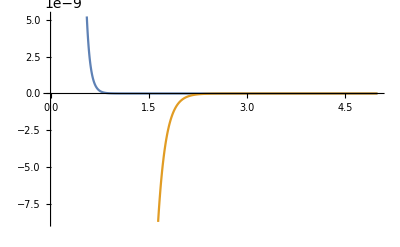

```mathematica
Clear[h,g,Kc,Ks]
Dh[x_]:=2x
Dg[x_,y_]:=1/2(x+y+1/y)
sol=NDSolve[
{
(* the RG-flow *)
h'[l]==h[l]*(2-Dh[ks0])-g[l]^2(kc0-ks0+1/ks0),g'[l]==g[l]*(2-Dg[kc0,ks0])-h[l]*g[l]*ks0,
(* initial conditions *)
h[0] == vperp/π,
g[0] ==- omega
},

{h,g},

{l,0,7},

Method->"ImplicitRungeKutta",
AccuracyGoal->100
]
Plot[Evaluate[{h[l],g[l]}/.sol[[1]]],{l,0,5}]
```